```mathematica
gammaSAS[r_,Rg_,d_]:=Module[
{b=Sqrt[d*(d+1)/2]},1/(4*Pi*Gamma[d])*b^3*Exp[-b*r/Rg]/(b*r/Rg)^(3-d)]
```

```mathematica
FullSimplify[4*Pi*Integrate[gammaSAS[r,Rg,d]r^2*Sinc[q*r],{r,0,Infinity},Assumptions->q≥0&&d>0&&Rg>0],Assumptions->q≥0&&d>0&&Rg>0]
```

(((2 q^2)/(d+d^2)+1/Rg^2)^(-d/2) Rg^(2-d) (-2 √2 √(d (1+d)) q Rg Cos[(1+d) ArcTan[(√2 q Rg)/(√(d (1+d)))]]+(d+d^2-2 q^2 Rg^2) Sin[(1+d) ArcTan[(√2 q Rg)/(√(d (1+d)))]]))/(√2 (-1+d) q √(d+d^2+2 q^2 Rg^2))

```mathematica
P[q_,Rg_,d_]:=(((2 q^2)/(d+d^2)+1/Rg^2)^(-d/2) Rg^(2-d) (-2 √2 √(d (1+d)) q Rg Cos[(1+d) ArcTan[(√2 q Rg)/(√(d (1+d)))]]+(d+d^2-2 q^2 Rg^2) Sin[(1+d) ArcTan[(√2 q Rg)/(√(d (1+d)))]]))/(√2 (-1+d) q √(d+d^2+2 q^2 Rg^2))
```

```mathematica
FullSimplify[Limit[P[q,Rg,d],d->1],Assumptions->q>0&&Rg>0]
```

(Rg^2 ArcTan[q Rg])/q

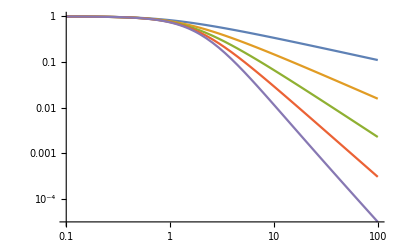

```mathematica
LogLogPlot[{P[q,1,0.5],(1^2 ArcTan[q 1])/q,P[q,1,1.5],P[q,1,2],P[q,1,2.5]},{q,0.1,100}]
```

```mathematica
gammaHB[r_,Rg_,C_]:=Module[
{a=Sqrt[6/(C+1)]},1/(8*Pi)*a^3*Exp[-a*r/Rg]*((1-C)/(1+C)+4*C/(1+C)*1/(a*r/Rg))]
```

```mathematica
FullSimplify[4*Pi*Integrate[gammaHB[r,Rg,C]r^2*Sinc[q*r],{r,0,Infinity},Assumptions->q≥0&&C>0&&Rg>0],Assumptions->q≥0&&C>0&&Rg>0]
```

(12 Rg^3 (3+C q^2 Rg^2))/((6+(1+C) q^2 Rg^2)^2)

```mathematica
Phb[u_,C_]:=(1+C*u^2/3)/(1+(C+1)*u^2/6)^2
```

```mathematica
PDBfract[u_,d_]:=(Sin[(d-1)*ArcTan[u]]/((d-1)*u*(1+u^2)^((d-1)/2)))^2
```

```mathematica
Plinfract[u_,d_]:=(Sin[(d-1)*ArcTan[u]]/((d-1)*u*(1+u^2)^((d-1)/2)))
```

```mathematica
Phbfract[q_,Rg_,d_,C_]:=Module[{xib2=(C+1)/(d*(d+1))*Rg^2,xil2=2*C/(d*(d+1))*Rg^2,u=q*Rg},PDBfract[Sqrt[xib2*q^2],d]/Plinfract[Sqrt[xil2*q^2],d]]
```

```mathematica
FullSimplify[Limit[Phbfract[q,Rg,d,C],C->0]/.q->u/Rg,Assumptions->d>0&&Rg>0&&u≥0]
```

((d (1+d))^d (d+d^2+u^2)^(1-d) Sin[(-1+d) ArcTan[u/(√(d (1+d)))]]^2)/((-1+d)^2 u^2)

```mathematica
FullSimplify[Limit[Phbfract[q,Rg,d,C],C->1]/. q->u/Rg,Assumptions->d>0&&u>0&&q≥0]
```

(√(d+d^2+2 u^2) (1+(2 u^2)/(d+d^2))^(-d/2) Sin[(-1+d) ArcTan[(√2 u)/(√(d (1+d)))]])/(√2 (-1+d) u)

```mathematica
FullSimplify[Limit[Phbfract[q,Rg,d,C],d->1],Assumptions->C>0&&q>0&&Rg>0]
```

(2 √C ArcTan[(√(1+C) q Rg)/(√2)]^2)/((1+C) q Rg ArcTan[√C q Rg])

```mathematica
FullSimplify[Limit[Phbfract[q,Rg,d,C],{C->0,d->1}],Assumptions->q>0&&Rg>0]
```

(2 ArcTan[(q Rg)/(√2)]^2)/(q^2 Rg^2)

```mathematica
FullSimplify[Limit[Phbfract[q,Rg,d,C],{C->1,d->1}],Assumptions->q>0&&Rg>0]
```

ArcTan[q Rg]/(q Rg)

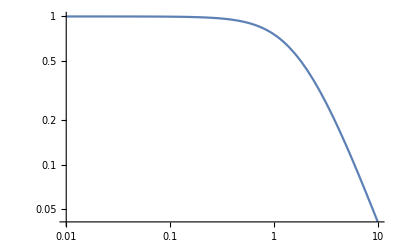

```mathematica
LogLogPlot[Phbfract[q,1,1.01,0.001],{q,0.01,10}]
```

```mathematica
Reduce[((ALPHA*(F-1)/(1-ALPHA*(F-1))+ALPHA/(1+ALPHA))/2.)<0,{F,ALPHA}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(F<0&&(-1.<ALPHA<1/(-1.+F)||ALPHA>0))||(0<F<1.&&(ALPHA<1/(-1.+F)||-1.<ALPHA<0))||(F==1.&&-1.<ALPHA<0)||(F>1.&&(-1.<ALPHA<0||ALPHA>1/(-1.+F)))

```mathematica
Reduce
```

```mathematica
S2z[ALPHA_,F_]:=((ALPHA*(F-1)/(1-ALPHA*(F-1))+ALPHA/(1+ALPHA))/2.)
```

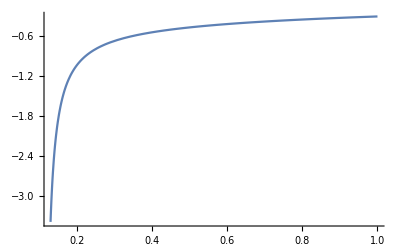

```mathematica
Plot[S2z[a,10],{a,0.13,1},PlotRange->All]
```

```mathematica
Pfhc[x_,alpha_,f_]:=(1+alpha*(f-1)/(1-alpha*(f-1))*(1-Exp[-x^2/6]))/(1-alpha/(1+alpha)*(1-Exp[-x^2/6]))
```

```mathematica
Pfhc[x_,alpha_,f_]:=(1-alpha*(f-1))/(1+alpha)*(1+alpha*Exp[-x^2/6])/(1-alpha*(f-1)*Exp[-x^2/6])
```

```mathematica
Pfhc[x_,alpha_,f_]:=(1-alpha/(1+alpha)*x^2/6)/(1+alpha*(f-1)/(1+alpha*(f-1))*x^2/6)
```

```mathematica
Pfhc[x_,alpha_,f_]:=Abs[(1-alpha*(f-1))/(alpha*f)*(alpha*f*Exp[-x^2/6])/(1-alpha*(f-1)*Exp[-x^2/6])]
```

```mathematica
Limit[Pfhc[x,alpha,f],x->Infinity]
```

0

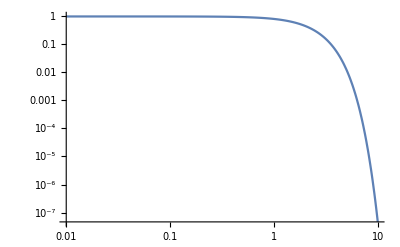

```mathematica
LogLogPlot[Pfhc[x,0.1,3],{x,0.01,10},PlotRange->All]
```